# Scattering Kernels in dD

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2019 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Isotropic Scattering

Isotropic scattering in dD can be sampled by taking the norm of an array of d normal random variates.  However, in odd dimensions, the cosine can be sampled in one step, given the roots to certain polynomials.

```mathematica
G[μ_,d_]:=((1-μ^2)^(1/2 (-3+d)))/(1/2 √π Gamma[1/2 (-1+d)] Gamma[d/2]^-1)
```

```mathematica
Integrate[1/2 G[u,d],{u,-1,k},Assumptions->d>1&&-1<k<1]
```

1/2+(k Gamma[d/2] Hypergeometric2F1[1/2,(3-d)/2,3/2,k^2])/(√π Gamma[1/2 (-1+d)])

### 3D

```mathematica
Solve[1/2+(k Gamma[d/2] Hypergeometric2F1[1/2,(3-d)/2,3/2,k^2])/(√π Gamma[1/2 (-1+d)])==x/.d->3,k]
```

{{k→-1+2 x}}

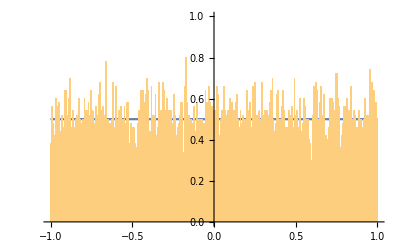

```mathematica
With[{d=3},
Show[
Plot[1/2 G[u,d] ,{u,-1,1}],
Histogram[
Table[
-1+2 RandomReal[]
,{i,Range[10000]}]
,500,"PDF"]
]
]
```

### 5D

```mathematica
Solve[1/2+(k Gamma[d/2] Hypergeometric2F1[1/2,(3-d)/2,3/2,k^2])/(√π Gamma[1/2 (-1+d)])==x/.d->5,k]/.x->#
```

{{k→-1/((-1+2 #1+2 √(-#1+#1^2))^(1/3))-(-1+2 #1+2 √(-#1+#1^2))^(1/3)},{k→(1+ⅈ √3)/(2 (-1+2 #1+2 √(-#1+#1^2))^(1/3))+1/2 (1-ⅈ √3) (-1+2 #1+2 √(-#1+#1^2))^(1/3)},{k→(1-ⅈ √3)/(2 (-1+2 #1+2 √(-#1+#1^2))^(1/3))+1/2 (1+ⅈ √3) (-1+2 #1+2 √(-#1+#1^2))^(1/3)}}

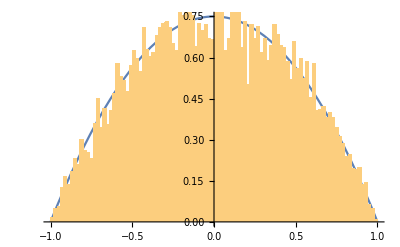

```mathematica
With[{d=5},
Show[
Plot[1/2 G[u,d] ,{u,-1,1}],
Histogram[
Table[
Chop[(1-ⅈ √3)/(2 (-1+2 #1+2 √(-#1+#1^2))^(1/3))+1/2 (1+ⅈ √3) (-1+2 #1+2 √(-#1+#1^2))^(1/3)&[RandomReal[]]]
,{i,Range[10000]}]
,100,"PDF"]
]
]
```

### 7D

```mathematica
Solve[1/2+(k Gamma[d/2] Hypergeometric2F1[1/2,(3-d)/2,3/2,k^2])/(√π Gamma[1/2 (-1+d)])==x/.d->7,k]
```

{{k→Root[8-16 x+15 #1-10 #1^3+3 #1^5&,1]},{k→Root[8-16 x+15 #1-10 #1^3+3 #1^5&,2]},{k→Root[8-16 x+15 #1-10 #1^3+3 #1^5&,3]},{k→Root[8-16 x+15 #1-10 #1^3+3 #1^5&,4]},{k→Root[8-16 x+15 #1-10 #1^3+3 #1^5&,5]}}

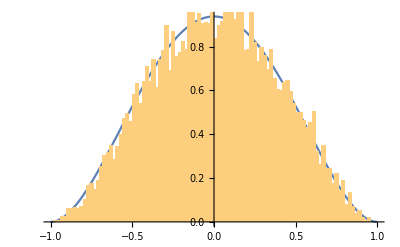

```mathematica
With[{d=7},
Show[
Plot[1/2 G[u,d] ,{u,-1,1}],
Histogram[
Table[
Chop[Root[8-16 RandomReal[]+15 #1-10 #1^3+3 #1^5&,1]]
,{i,Range[10000]}]
,100,"PDF"]
]
]
```

### 9D

```mathematica
Solve[1/2+(k Gamma[d/2] Hypergeometric2F1[1/2,(3-d)/2,3/2,k^2])/(√π Gamma[1/2 (-1+d)])==x/.d->9,k]
```

{{k→Root[-16+32 x-35 #1+35 #1^3-21 #1^5+5 #1^7&,1]},{k→Root[-16+32 x-35 #1+35 #1^3-21 #1^5+5 #1^7&,2]},{k→Root[-16+32 x-35 #1+35 #1^3-21 #1^5+5 #1^7&,3]},{k→Root[-16+32 x-35 #1+35 #1^3-21 #1^5+5 #1^7&,4]},{k→Root[-16+32 x-35 #1+35 #1^3-21 #1^5+5 #1^7&,5]},{k→Root[-16+32 x-35 #1+35 #1^3-21 #1^5+5 #1^7&,6]},{k→Root[-16+32 x-35 #1+35 #1^3-21 #1^5+5 #1^7&,7]}}

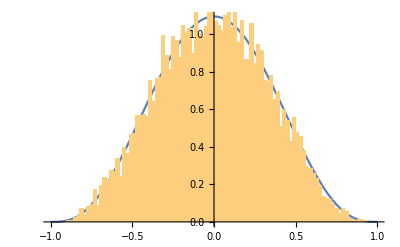

```mathematica
With[{d=9},
Show[
Plot[1/2 G[u,d] ,{u,-1,1}],
Histogram[
Table[
Chop[Root[-16+32 RandomReal[]-35 #1+35 #1^3-21 #1^5+5 #1^7&,2]]
,{i,Range[10000]}]
,100,"PDF"]
]
]
```